# Laplaceova transformacija

F(s)=∫_0^∞ f(t)ⅇ^-st ⅆt,s>0

```mathematica
f=t^2
Integrate[f E^(-s t),{t,0,∞}]
```

t^2

ConditionalExpression[2/s^3,Re[s]>0]

Pogoj, da nas rezultat zanima samo za s > 0, lahko zapišemo kot opcijo v ukaz Integrate.

```mathematica
f=t^2
Integrate[f E^(-s t),{t,0,∞},Assumptions->s>0]
```

t^2

2/s^3

Mathematica ima že vgrajene funkcije za Laplaceovo transformacijo.
Ukaza sta LaplaceTransform in InverseLaplaceTransform.

```mathematica
?LaplaceTransform
?InverseLaplaceTransform
```

```mathematica
f=t^2
LaplaceTransform[f,t,s]
InverseLaplaceTransform[%,s,t]
```

t^2

2/s^3

t^2

Poglejmo si Laplaceove transformacije nekaj osnovnih elementarnih funkcij.
Funkcijo Gamma, ki je tudi vgrajena v Mathematico bomo še spoznali na enih izmed naslednjih vaj:
Γ(x)=∫_0^∞ t^(x-1)ⅇ^-t ⅆt
velja: Γ(x+1)= x Γ(x)

{1/s,1/s^2,s^(-1-n) Gamma[1+n],1/(-a+s),ω/(s^2+ω^2),s/(s^2+ω^2)}

n!

n!

True

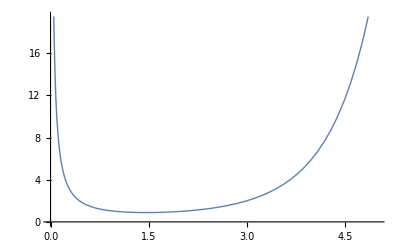

```mathematica
LaplaceTransform[{1,t,t^n,E^(a t),Sin[ω t],Cos[ω t]},t,s]
FullSimplify[Gamma[n+1],Assumptions->n∈Integers && n>0]
FullSimplify[Gamma[n+1],Assumptions->n∈PositiveIntegers ]
FullSimplify[Gamma[x+1]==x Gamma[x]]
Plot[Gamma[x],{x,0,5},PlotStyle->Thick]
```

Dogovora o pisavi ℒ[ f(t) ] = F[s] Mathematica seveda ne pozna.
Po želji lahko to pisavo posredujemo Mathematici z operatorjem /.

```mathematica
LaplaceTransform[x[t],t,s]
LaplaceTransform[x[t],t,s]/.LaplaceTransform[x[t],t,s]->X[s]
```

LaplaceTransform[x[t],t,s]

X[s]

1. Izračunajte Laplaceovo transformiranko funkcije
                f (t) = { t | , če
2-t | , če     0≤ t ≤ 1
1< t < 2 
                f(t+2)=f(t)

Rezultat:1/s^2 Tanh[s/2]

Transformiranka periodične funkcije f(t) s periodo T, torej f(t+T) = f(t), je:
F(s) = 1/(1-ⅇ^-sT)∫_0^T ⅇ^-st f(t)ⅆt

Piecewise[{{t, 0≤t≤1}, {2-t, 1<t<2}, {0, True}}]

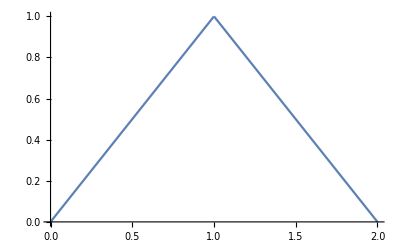

2

(ⅇ^(-2 s) (-1+ⅇ^s)^2)/((1-ⅇ^(-2 s)) s^2)

(-1+ⅇ^s)/((1+ⅇ^s) s^2)

Tanh[s/2]/s^2

```mathematica
Clear[f]
f= Piecewise[{{t, 0≤ t≤ 1},{2-t,1<t<2}}]
Plot[f,{t,0,2}]
T=2
F= (1/(1-E^(-s T))) Integrate[f* E^(-s t), {t,0,T}]
Simplify[F]
FullSimplify[F]
```

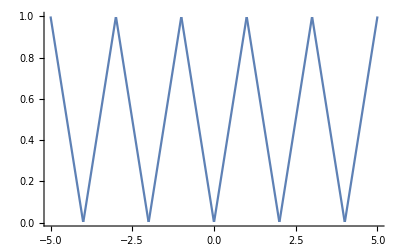

Tanh[s/2]/s^2

```mathematica
Clear[f,ff]
f[t_]:=Piecewise[{{t,0≤t≤1},{2-t,1<t<2}}]
ff[t_]:=f[Mod[t,2]]
Plot[ff[t],{t,-5,5},PlotRange->All]
LaplaceTransform[ff[t],t,s]
```

2. Izračunajte inverzno Laplaceovo transformiranko funkcije
                                                   F(s)=1/((s^2+1)^2)
     na tri načine:
     1. z ukazom InverseLaplaceTransform
     2. z inverzno formulo ∑Res(F(s)e^st)
     3. s pravilom o konvoluciji f(t)=ℒ^-1[1/(s^2+1)] * ℒ^-1[1/(s^2+1)]

Konvolucija:
 (f*g)(t) = ∫_0^t f(u) g(u-t)ⅆu
ℒ[(f*g)(t) ] = ℒ [f(t)] - ℒ [g(t)]

Rezultat:1/2 (sin t-t cos t)

```mathematica
F = 1/(s^2 + 1)^2
InverseLaplaceTransform[F, s,t]

(*Bromwicheva formula: najprej iščemo kje je imenovalec enak nič = singularne točke*)

Solve[Denominator[F]==0,s] (*kdaj je imenovalec enak 0*)
Simplify[ComplexExpand[Residue[F* E^(s t), {s, -I}] + Residue[F* E^(s t), {s, I}] ]]

(*Pravilo o konvoluciji:
bomo razbili na dva dela:
F(s)= G[s] G[s], G(s) = 1/(s^2 + 1)
f[t]= (g*g)(t); G(s) = ℒ(g(s))*)

g[u_] := InverseLaplaceTransform[1/(s^2 + 1), s, u]
Integrate[g[u]*g[u-t],{u,0,t}]
```

1/((1+s^2)^2)

1/2 (-t Cos[t]+Sin[t])

{{s→-ⅈ},{s→-ⅈ},{s→ⅈ},{s→ⅈ}}

1/2 (-t Cos[t]+Sin[t])

1/2 (t Cos[t]-Sin[t])

3. S pomočjo Laplaceove transformacije rešite diferencialno enačbo
                                                   y'''-2y''+y'=4
      pri začetnih vrednostih
                                 y''(0)=1, y'(0)=2 in y(0)=-2.

Rezultat:y(t)=3-5 ⅇ^t+4 t+3 ⅇ^t t

Reševanje diferencialnih enačb z Laplacovo transformacijo :
1. Originalno enačbo transformiramo.
2. Rešimo transformirano enačbo.
3. Inverzna transformacija rešitve.

```mathematica
(*1 korak*)LaplaceTransform[y'''[t] - 2 y''[t] + y'[t] ==4, t,s]/. LaplaceTransform[y[t],t,s]-> Y[s] /. y[0]-> -2 /.  y'[0]-> 2 /. y''[0]-> 1

(*2 korak*)
Y[s]/. Flatten[Solve[%, Y[s]]]

(*3 korak*)
InverseLaplaceTransform[%,s,t]
```

1-2 s+2 s^2+s Y[s]+s^3 Y[s]-2 (-2+2 s+s^2 Y[s])==4/s

(4-5 s+6 s^2-2 s^3)/((-1+s)^2 s^2)

3-5 ⅇ^t+4 t+3 ⅇ^t t

### Primeri nalog za preverjanje

4. S pomočjo Laplaceove transformacije rešite diferencialno enačbo
                                            x'' + 2 x' + 2 x = 0
     pri začetnih vrednostih
                                        x(0) = 1 in x' (0) = -1.
     Koliko je x(1)?

Rezultat: 0.198766

```mathematica
(*1 korak*)Simplify[LaplaceTransform[x''[t] + 2 x'[t] + 2x[t] ==0, t,s]/. LaplaceTransform[x[t],t,s]-> X[s] /. x[0]-> 1 /.  x'[0]-> -1]

(*2 korak*)
X[s]/. Flatten[Solve[%, X[s]]]

(*3 korak*)
FullSimplify[InverseLaplaceTransform[%,s,t]]
%/. t-> 1.
%/. t-> 1//N
```

(2+2 s+s^2) X[s]==1+s

(1+s)/(2+2 s+s^2)

ⅇ^-t Cos[t]

0.198766

0.198766

```mathematica
(***************************************************************************)
DSolve[{x''[t]+2 x'[t]+2 x[t]==0,x[0]==1,x'[0]==-1},x[t],t]/.t->1//N
```

{{x[1.]→0.198766}}

5. S pomočjo Laplaceove transformacije rešite robni problem
                                                     x''+3x'+4x=ⅇ^t
      pri (robnih) vrednostih
                                                 x(0)=1 in x(2)=3.5.
     Koliko je x(1)?

Rezultat: 24.2645

```mathematica
(*1 korak, rečemo da je odvod neznanka A*)Simplify[LaplaceTransform[x''[t] + 3 x'[t] + 4 x[t] == E^t, t,s]/. LaplaceTransform[x[t],t,s]-> X[s] /. x[0]-> 1 /.  x'[0]-> A]

(*2 korak*)
X[s]/. Flatten[Solve[%, X[s]]]



(*3 korak, poiščemo. vstavimo x in solve. OBOJE VSTAVIMO NOT *)
FullSimplify[InverseLaplaceTransform[%,s,t]]
A/. Flatten[Solve[(%/. t-> 2)== 3.5, A]]
%%/. t-> 1. /. A-> %
```

(4+3 s+s^2) X[s]==3+A+1/(-1+s)+s

(-2-A+2 s+A s+s^2)/((-1+s) (4+3 s+s^2))

1/56 ⅇ^(-3 t/2) (7 ⅇ^(5 t/2)+49 Cos[(√7 t)/2]+√7 (19+16 A) Sin[(√7 t)/2])

144.836

24.2645

6. Poiščite funkcijo x(t), ki reši integralsko enačbo -ISTE TRI ENAČBE
                               x(t) = 1+1/2∫_0^t sin2(t-u) x(u)ⅆu

Rezultat: x(t)=(4-cos √3 t)/3

```mathematica
(*1 korak*)Simplify[LaplaceTransform[x[t] == 1+ Integrate[Sin [2(t-u)] x[u], {u, 0, t}]/2, t,s]/. LaplaceTransform[x[t],t,s]-> X[s] ]

(*2 korak*)
X[s]/. Flatten[Solve[%, X[s]]]

(*3 korak*)
FullSimplify[InverseLaplaceTransform[%,s,t]]
```

X[s]==1/s+X[s]/(4+s^2)

(4+s^2)/(s (3+s^2))

1/3 (4-Cos[√3 t])

7. S pomočjo Laplaceove transformacije rešite sistem diferencialnih enačb
                                                     x'=y-z
                                                     y'=x+z
                                                     z'=y-x
pri začetnih vrednostih
                            x(0)=1, y(0)=0 in z(0)=-1.

Rezultat: x(t)=ⅇ^t, y(t)=0, z(t)=-e^t

```mathematica
(*1 korak*)
Clear [x,y,z]
Simplify[LaplaceTransform[{x'[t]==  y[t] - z[t], y'[t]== x[t]+z[t], z'[t]== y[t]- x[t]}, t,s]/. LaplaceTransform[x[t],t,s]-> X[s] ] /. LaplaceTransform[z[t],t,s] -> Z[s] /. LaplaceTransform[y[t],t,s] -> Y[s]/. x[0]-> 1 /. y[0]-> 0 /. z[0] -> -1

(*2 korak*)
{X[s], Y[s],Z[s]}/. Flatten[Solve[%, {X[s],Y[s], Z[s]}]]

(*3 korak*)
FullSimplify[InverseLaplaceTransform[%,s,t]]
```

{1+Y[s]==s X[s]+Z[s],s Y[s]==X[s]+Z[s],-1+Y[s]==X[s]+s Z[s]}

{-1/(1-s),0,-1/(-1+s)}

{ⅇ^t,0,-ⅇ^t}

```mathematica
(***************************************************************************)
DSolve[{x'[t]==y[t]-z[t],y'[t]==x[t]+z[t],z'[t]==y[t]-x[t],x[0]==1,y[0]==0,z[0]==-1},{x[t],y[t],z[t]},t]
```

{{x[t]→ⅇ^t,y[t]→0,z[t]→-ⅇ^t}}